## Cancel a sinusoidal disturbance using a disturbance estimator (Problem 4.10)

First-order dynamics with  sine-wave disturbance.

```mathematica
Clear["Global`*"]                                              (* clear everything *)
```

```mathematica
A0 ={{-1}} ;B0 ={{1}}; C0={{1}};        (* physical dynamics *)
```

```mathematica
Ad = ({{0, 1}, {-1, 0}}); Bd =({{0}, {0}}); Cd = ({{1, 0}});   (* disturbance dynamics *)
```

```mathematica
sysd = StateSpaceModel[{Ad,Bd,Cd}];
```

```mathematica
K0 = {{2}};                                        (* state-vector controller gains *)
```

```mathematica
Ld = EstimatorGains[sysd,{-4,-4}]  (* disturb observ. gains *)
```

{{8},{15}}

```mathematica
L0 = {{4}};                      (* observer gains for state disturbance. *)
```

```mathematica
bigA = ArrayFlatten[({{A0, B0.Cd, -B0.K0, -B0.Cd}, {({{0}, {0}}), Ad, ({{0}, {0}}), ({{0, 0}, {0, 0}})}, {L0.C0, ({{0, 0}}), A0-B0.K0-L0.C0, ({{0, 0}})}, {Ld.C0, ({{0, 0}, {0, 0}}), -Ld.C0, Ad}}) ];
```

```mathematica
bigA//MatrixForm
```

(-1 | 1 | 0 | -2 | -1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
4 | 0 | 0 | -7 | 0 | 0
8 | 0 | 0 | -8 | 0 | 1
15 | 0 | 0 | -15 | -1 | 0)

```mathematica
bigB = ({{0}, {0}, {0}, {0}, {0}, {0}});
```

```mathematica
sys0 = StateSpaceModel[{bigA,bigB}]  (* only need bigA and bigB; *)
```

-110-2-10000100000-100000400-7000800-80101500-15-100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1-661FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Eigenvalues[bigA]//N
```

{-4.,-3.,-0.5+2.17945 ⅈ,-0.5-2.17945 ⅈ,0.+1. ⅈ,0.-1. ⅈ}

```mathematica
tmax = 15;
```

```mathematica
{x,d,dd,xh,dh,ddh} = StateResponse[{sys0,{-1,1,0,0,0,0}},0,{t,0,tmax}];
```

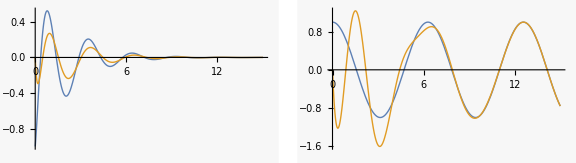

```mathematica
p1=Plot[{x,xh},{t,0,tmax},PlotRange->Full] ;
p2=Plot[{d,dh},{t,0,tmax}];
GraphicsRow[{p1,p2},ImageSize->Large]
```